# Modified Gravity Models

## f(R)

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
dir="./Data/fR/";
DatafRp=Import[dir<>"fR_p_pk.dat","Table"][[5;;-1]];
DatafRpp=Import[dir<>"fR_pp_pk.dat","Table"][[5;;-1]];
DatafRppp=Import[dir<>"fR_ppp_pk.dat","Table"][[5;;-1]];
DatafRpppp=Import[dir<>"fR_pppp_pk.dat","Table"][[5;;-1]];
```

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
AS2=0.00837;
kS2=0.081;
σS2=0.0404;
AS3=0.012538;
kS3=0.14376;
σS3=0.007586;
AS4=0.0038985;
kS4=1.1791;
σS4=0.3;

q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)

fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]
PS2[k_]:=1+AS2*ⅇ^(-((k-kS2)/σS2)^2)
PS3[k_]:=1-AS3*ⅇ^(-((k-kS3)/σS3)^2)
PS4[k_]:=1-AS4*ⅇ^(-((k-kS4)/σS4)^2)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,αMG_,γMG_,kMG_,σMG_]:=A0[h,ωm,ns,As]*(1+0.711 αMG^3+1.880 αMG^4+0.939 αMG^5)k^ns*Tnw[k,h,ωb,ωm]^2(1+γMG/(1+(kMG/k)^σMG))
Plarge[k_,h_,ωm_,ns_,As_,sMG_]:=A0[h,ωm,ns,As]*(1+sMG)*k^ns; (* Primordial spectrum *)
σT[k_,kT_,βT_]:=1/(1+ⅇ^(-(Log[k]-Log[kT])/βT)); (* Transition function *)
 (* Non-Wiggles Subscript[P, MG] *)
PMGnw[k_,h_,ωb_,ωm_,ns_,As_,αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=(1-σT[k,kT,βT])Plarge[k,h,ωm,ns,As,sMG]+σT[k,kT,βT]*Psmall[k,h,ωb,ωm,ns,As,αMG,γMG,kMG,σMG]
(* Total spectrum *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=(1-σT[k,kT,βT])Plarge[k,h,ωm,ns,As,sMG]+σT[k,kT,βT]*Psmall[k,h,ωb,ωm,ns,As,αMG,γMG,kMG,σMG]*Tw[k,h,ωb,ωm]^2*PS2[k]*PS3[k]*PS4[k]
```

### Accuracy

```mathematica
h=0.6711;
Ωb=0.049;
ωb=Ωb*h^2;
Ωm=0.3175;
ωm=Ωm*h^2;
ns=0.9624;
As=2.130397;
```

```mathematica
χ2fRp[αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=Mean[Table[Abs[1-PMGnw[DatafRp[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/DatafRp[[i,2]]]*100,{i,1,Length[DatafRp]}]];
χ2fRpp[αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=Mean[Table[Abs[1-PMGnw[DatafRpp[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/DatafRpp[[i,2]]]*100,{i,1,Length[DatafRpp]}]];
χ2fRppp[αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=Mean[Table[Abs[1-PMGnw[DatafRppp[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/DatafRppp[[i,2]]]*100,{i,1,Length[DatafRppp]}]];
χ2fRpppp[αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=Mean[Table[Abs[1-PMGnw[DatafRpppp[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/DatafRpppp[[i,2]]]*100,{i,1,Length[DatafRpppp]}]];
```

```mathematica
ParamsfRp=NMinimize[χ2fRp[αMG,kT,βT,sMG,γMG,kMG,σMG],{αMG,kT,βT,sMG,γMG,kMG,σMG},Method->"DifferentialEvolution",MaxIterations->2000]//Quiet
ParamsfRpp=NMinimize[χ2fRpp[αMG,kT,βT,sMG,γMG,kMG,σMG],{αMG,kT,βT,sMG,γMG,kMG,σMG},Method->"DifferentialEvolution",MaxIterations->2000]//Quiet
ParamsfRppp=NMinimize[χ2fRppp[αMG,kT,βT,sMG,γMG,kMG,σMG],{αMG,kT,βT,sMG,γMG,kMG,σMG},Method->"DifferentialEvolution",MaxIterations->2000]//Quiet
ParamsfRpppp=FindMinimum[χ2fRpppp[αMG,kT,βT,sMG,γMG,kMG,σMG],{{αMG,0.37},{kT,0.01},{βT,0.4},{sMG,-0.4},{γMG,-1},{kMG,0.8},{σMG,-0.81}},MaxIterations->2000]//Quiet
```

{1.55944,{αMG→-0.367582,kT→0.000676078,βT→0.44064,sMG→-0.378433,γMG→-0.375892,kMG→1.85192,σMG→-1.3864}}

{1.52218,{αMG→-0.368282,kT→0.00065329,βT→0.439712,sMG→-0.378395,γMG→-0.376115,kMG→0.641704,σMG→-1.26353}}

{1.47051,{αMG→-0.0843604,kT→0.0014941,βT→0.524328,sMG→-0.378276,γMG→-0.401443,kMG→0.242016,σMG→-0.985918}}

{1.84791,{αMG→0.661416,kT→0.00229654,βT→0.51141,sMG→-0.378257,γMG→-0.675652,kMG→0.659823,σMG→-0.621102}}

```mathematica
MAPEfRp=Table[{DatafRp[[i,1]],Abs[1-(PMG[DatafRp[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRp[[2]])/DatafRp[[i,2]]]*100},{i,1,Length[DatafRp]}]//Quiet;
MAPEfRpp=Table[{DatafRpp[[i,1]],Abs[1-(PMG[DatafRpp[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRpp[[2]])/DatafRpp[[i,2]]]*100},{i,1,Length[DatafRpp]}]//Quiet;
MAPEfRppp=Table[{DatafRppp[[i,1]],Abs[1-(PMG[DatafRppp[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRppp[[2]])/DatafRppp[[i,2]]]*100},{i,1,Length[DatafRppp]}]//Quiet;
MAPEfRpppp=Table[{DatafRpppp[[i,1]],Abs[1-(PMG[DatafRpppp[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRpppp[[2]])/DatafRpppp[[i,2]]]*100},{i,1,Length[DatafRpppp]}]//Quiet;
```

```mathematica
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@MAPEfRp[[1;;-4,2]]
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@MAPEfRpp[[1;;-4,2]]
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@MAPEfRppp[[1;;-4,2]]
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@MAPEfRpppp[[1;;-4,2]]
```

{0.481743,0.248726,0.402581,1.63622}

{0.565421,0.394005,0.67392,1.63847}

{0.441782,0.291854,0.573294,1.18396}

{1.02417,0.948795,1.37143,2.31484}

### Visual Comparison

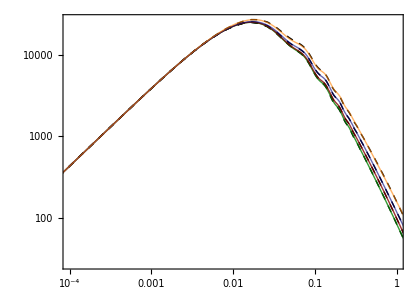

```mathematica
ListLogLogPlot[{DatafRp,DatafRpp,DatafRppp,DatafRpppp},Joined->True,PlotRange->{{10^-4,1}//Log,All},PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [ (\\text{Mpc} \\, h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},AspectRatio->0.7,ImageSize->420];
LogLogPlot[{PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRp[[2]],
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRpp[[2]],
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRppp[[2]],
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRpppp[[2]]}//Evaluate,{k,10^-5,1.5},PlotRange->All,PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]],
Directive[Thick,Opacity[0.6],Orange]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [(\\text{Mpc} \\, h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = 5 \\times 10^{-7}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = 5 \\times 10^{-6}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = 5 \\times 10^{-5}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = 5 \\times 10^{-4}"]},
 LegendLayout->{"Row",4},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.37}],ImageSize->420];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},PlotRange->{{10^-4,1}//Log,All},ImageSize->420,AspectRatio->0.7]//Quiet
```

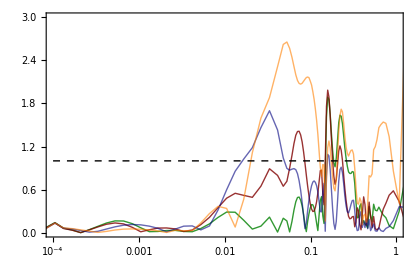

```mathematica
ListLogLinearPlot[{MAPEfRp,MAPEfRpp,MAPEfRppp,MAPEfRpppp},Joined->True,PlotRange->{{10^-4,1},{0,3}},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]],
Directive[Thick,Opacity[0.6],Orange]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]}},ImageSize->420,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = 5 \\times 10^{-7}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = 5 \\times 10^{-6}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = 5 \\times 10^{-5}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = 5 \\times 10^{-4}"]},
 LegendLayout->{"Row", 4},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.24,0.53}]]//Quiet
```

```mathematica
PkfRp=Interpolation[DatafRp];
PkfRpp=Interpolation[DatafRpp];
PkfRppp=Interpolation[DatafRppp];
PkfRpppp=Interpolation[DatafRpppp];
```

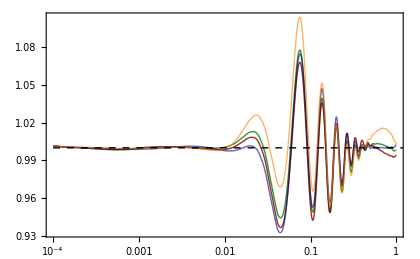

```mathematica
LogLinearPlot[{PkfRp[k]/PMGnw[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRp[[2]],
PkfRpp[k]/PMGnw[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRpp[[2]],
PkfRppp[k]/PMGnw[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRppp[[2]],
PkfRpppp[k]/PMGnw[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsfRpppp[[2]]},{k,10^-4,1},PlotRange->{{10^-4,1},All},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]],
Directive[Thick,Opacity[0.6],Orange]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","O_\\text{lin}(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]}},ImageSize->420,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = -5 \\times 10^{-7}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = -5 \\times 10^{-6}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = -5 \\times 10^{-5}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["f_{R_0} = -5 \\times 10^{-4}"]},
 LegendLayout->{"Row", 4},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.25,0.58}]]
```

## plk_late

```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

### Data

```mathematica
dir="./Data/plk_late/";
DataE110E221=Import[dir<>"E11_0_E22_1_pk.dat","Table"][[5;;-1]];
DataE1105E2205=Import[dir<>"E11_0.5_E22_0.5_pk.dat","Table"][[5;;-1]];
DataE1105nE2205n=Import[dir<>"E11_0.5n_E22_0.5n_pk.dat","Table"][[5;;-1]];
DataE111E221=Import[dir<>"E11_1_E22_1_pk.dat","Table"][[5;;-1]];
DataE111nE221n=Import[dir<>"E11_1n_E22_1n_pk.dat","Table"][[5;;-1]];
```

### Fitting Function

```mathematica
c=2998;
kpivot=0.05;
A0[h_,ωm_,ns_,As_]:=2 π^2*(As*10^-9)*(h/kpivot)^(ns-1)*((2*c^2*h^2)/(5ωm))^2;
a1=101.855;
a2=21112.189;
a3=35913.065;
a4=1428.081;
a5=1.03922;
a6=1.36418;
a7=0.78991;
a8=0.5426;
a9=0.7349;
a10=0.10047;
a11=0.1485;
a12=0.0005236;
a13=49.99978;
a14=46.02641;
a15=1.0049;
b1=1.483;
b2=3.972;
b3=6.097;
b4=7.507;
b5=2.7345;
b6=0.9914;
b7=0.26955;
b8=1.19806;
b9=0.739668;
b10=0.76324;
b11=1.49987;
b12=1.47345;
b13=0.96164;
b14=1.24458;
b15=0.234948;

c1=0.00785436;
c2=0.177084;
c3=0.00912388;
c4=0.618711;
c5=11.9611;
c6=2.81343;
c7=0.784719;

AS1=0.006249;
kS1=0.199435;
σS1=0.062686;
AS2=0.00837;
kS2=0.081;
σS2=0.0404;
AS3=0.012538;
kS3=0.14376;
σS3=0.007586;
AS4=0.0038985;
kS4=1.1791;
σS4=0.3;

q[k_,h_,ωb_,ωm_]:=(h*k)/(ωm-ωb)
Tnw[k_,h_,ωb_,ωm_]:=(1+a1*q[k,h,ωb,ωm]^b1+a2*q[k,h,ωb,ωm]^b2+ a3*q[k,h,ωb,ωm]^b3+a4*q[k,h,ωb,ωm]^b4)^(-1/4)

fα[ωb_,ωm_]:=a10-a11*ωb^b10+a12*ωm^b11
fβ[ωb_,ωm_]:=b12-a13*ωb^b13+a14*ωm^b14
fnode[ωm_]:=a15*ωm^b15 
sGA[ωb_,ωm_]:=1/(c1*ωb^c2+c3*ωm^c4+c5*ωb^c6*ωm^c7)
kSilk[ωb_,ωm_]:=0.373 ωb^0.419+0.195 ωm^1.0957
Tw[k_,h_,ωb_,ωm_]:=1+fα[ωb,ωm]/(a5+(fβ[ωb,ωm]/(k*h*sGA[ωb,ωm]))^b5)*ⅇ^(-a6(k*h/kSilk[ωb,ωm])^b6)*Sin[a7(k*h*sGA[ωb,ωm]+a8*ωm^-b7)/((a9+(fnode[ωm]/(k*h*sGA[ωb,ωm]))^b8)^b9)]
TS1[k_]:=1-AS1*ⅇ^(-((k-kS1)/σS1)^2)
TGA[k_,h_,ωb_,ωm_]:=Tnw[k,h,ωb,ωm]*Tw[k,h,ωb,ωm]*TS1[k]
PS2[k_]:=1+AS2*ⅇ^(-((k-kS2)/σS2)^2)
PS3[k_]:=1-AS3*ⅇ^(-((k-kS3)/σS3)^2)
PS4[k_]:=1-AS4*ⅇ^(-((k-kS4)/σS4)^2)
Psmall[k_,h_,ωb_,ωm_,ns_,As_,αMG_,γMG_,kMG_,σMG_]:=A0[h,ωm,ns,As]*(1+0.711 αMG^3+1.880 αMG^4+0.939 αMG^5)k^ns*Tnw[k,h,ωb,ωm]^2(1+γMG/(1+(kMG/k)^σMG))
Plarge[k_,h_,ωm_,ns_,As_,sMG_]:=A0[h,ωm,ns,As]*(1+sMG)*k^ns; (* Primordial spectrum *)
σT[k_,kT_,βT_]:=1/(1+ⅇ^(-(Log[k]-Log[kT])/βT)); (* Transition function *)
 (* Non-Wiggles Subscript[P, MG] *)
PMGnw[k_,h_,ωb_,ωm_,ns_,As_,αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=(1-σT[k,kT,βT])Plarge[k,h,ωm,ns,As,sMG]+σT[k,kT,βT]*Psmall[k,h,ωb,ωm,ns,As,αMG,γMG,kMG,σMG]
(* Total spectrum *)
PMG[k_,h_,ωb_,ωm_,ns_,As_,αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=(1-σT[k,kT,βT])Plarge[k,h,ωm,ns,As,sMG]+σT[k,kT,βT]*Psmall[k,h,ωb,ωm,ns,As,αMG,γMG,kMG,σMG]*Tw[k,h,ωb,ωm]^2*PS2[k]*PS3[k]*PS4[k]
```

### Accuracy

```mathematica
h=0.67810;
ωb=0.02238280;
ωc=0.1201075;
ωm=ωc+ωb;
ns=0.9660499;
As=2.100549;
```

```mathematica
χ2E110E221[αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=Mean[Table[Abs[1-PMGnw[DataE110E221[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/DataE110E221[[i,2]]]*100,{i,1,Length[DataE110E221]}]];
χ2E1105E2205[αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=Mean[Table[Abs[1-PMGnw[DataE1105E2205[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/DataE1105E2205[[i,2]]]*100,{i,1,Length[DataE1105E2205]}]];
χ2E1105nE2205n[αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=Mean[Table[Abs[1-PMGnw[DataE1105nE2205n[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/DataE1105nE2205n[[i,2]]]*100,{i,1,Length[DataE1105nE2205n]}]];
χ2E111E221[αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=Mean[Table[Abs[1-PMGnw[DataE111E221[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/DataE111E221[[i,2]]]*100,{i,1,Length[DataE111E221]}]];
χ2E111nE221n[αMG_,kT_,βT_,sMG_,γMG_,kMG_,σMG_]:=Mean[Table[Abs[1-PMGnw[DataE111nE221n[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/DataE111nE221n[[i,2]]]*100,{i,1,Length[DataE111nE221n]}]];
```

```mathematica
ParamsE110E221=FindMinimum[χ2E110E221[αMG,kT,βT,sMG,γMG,kMG,σMG],{{αMG,0.37},{kT,0.01},{βT,0.4},{sMG,-0.4},{γMG,-1},{kMG,0.8},{σMG,-0.81}},MaxIterations->1000]//Quiet
ParamsE1105E2205=FindMinimum[χ2E1105E2205[αMG,kT,βT,sMG,γMG,kMG,σMG],{{αMG,0.37},{kT,0.01},{βT,0.4},{sMG,-0.4},{γMG,-1},{kMG,0.8},{σMG,-0.81}},MaxIterations->1000]//Quiet
ParamsE1105nE2205n=FindMinimum[χ2E1105nE2205n[αMG,kT,βT,sMG,γMG,kMG,σMG],{{αMG,0.37},{kT,0.01},{βT,0.4},{sMG,-0.4},{γMG,-1},{kMG,0.8},{σMG,-0.81}},MaxIterations->1000]//Quiet
ParamsE111E221=FindMinimum[χ2E111E221[αMG,kT,βT,sMG,γMG,kMG,σMG],{{αMG,0.37},{kT,0.01},{βT,0.4},{sMG,-0.4},{γMG,-1},{kMG,0.8},{σMG,-0.81}},MaxIterations->1000]//Quiet
ParamsE111nE221n=FindMinimum[χ2E111nE221n[αMG,kT,βT,sMG,γMG,kMG,σMG],{{αMG,-0.7},{kT,0.01},{βT,0.4},{sMG,-0.4},{γMG,-1},{kMG,0.8},{σMG,-0.81}},MaxIterations->1000]//Quiet
```

{1.40995,{αMG→-0.740677,kT→0.000709528,βT→0.502381,sMG→-0.701226,γMG→-0.856447,kMG→1.26848,σMG→-0.0000265978}}

{1.41582,{αMG→-0.741104,kT→0.000766319,βT→0.494192,sMG→-0.771487,γMG→-0.753039,kMG→1.13665,σMG→-0.00161761}}

{1.42232,{αMG→-0.775707,kT→0.000281436,βT→0.513162,sMG→1.44766,γMG→-0.963011,kMG→1.43692,σMG→0.00213225}}

{1.44017,{αMG→-0.779242,kT→0.00103996,βT→0.472649,sMG→-0.894277,γMG→-0.672904,kMG→1.02771,σMG→-0.0049334}}

{1.45655,{αMG→-0.757452,kT→0.00011401,βT→0.47698,sMG→23.9008,γMG→-1.03135,kMG→1.48848,σMG→0.00109876}}

```mathematica
MAPEE110E221=Table[{DataE110E221[[i,1]],Abs[1-(PMG[DataE110E221[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE110E221[[2]])/DataE110E221[[i,2]]]*100},{i,1,Length[DataE110E221]}]//Quiet;
MAPEE1105E2205=Table[{DataE1105E2205[[i,1]],Abs[1-(PMG[DataE1105E2205[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE1105E2205[[2]])/DataE1105E2205[[i,2]]]*100},{i,1,Length[DataE1105E2205]}]//Quiet;
MAPEE111E221=Table[{DataE111E221[[i,1]],Abs[1-(PMG[DataE111E221[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE111E221[[2]])/DataE111E221[[i,2]]]*100},{i,1,Length[DataE111E221]}]//Quiet;
MAPEE1105nE2205n=Table[{DataE1105nE2205n[[i,1]],Abs[1-1/DataE1105nE2205n[[i,2]](PMG[DataE1105nE2205n[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE1105nE2205n[[2]])]*100},{i,1,Length[DataE1105nE2205n]}]//Quiet;
MAPEE111nE221n=Table[{DataE111nE221n[[i,1]],Abs[1-(PMG[DataE111nE221n[[i,1]],h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE111nE221n[[2]])/DataE111nE221n[[i,2]]]*100},{i,1,Length[DataE111nE221n]}]//Quiet;
```

```mathematica
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@MAPEE111E221[[1;;-4,2]]
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@MAPEE111nE221n[[1;;-4,2]]
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@MAPEE1105E2205[[1;;-4,2]]
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@MAPEE1105nE2205n[[1;;-4,2]]
{Mean[#],Median[#],Quantile[#,0.68],Quantile[#,0.95]}&@MAPEE110E221[[1;;-4,2]]
```

{0.219429,0.161696,0.196614,0.774503}

{0.2622,0.187797,0.293232,0.868632}

{0.191207,0.10658,0.166303,0.717187}

{0.235662,0.198292,0.250253,0.627684}

{0.186483,0.119919,0.1766,0.651612}

### Visual Comparison

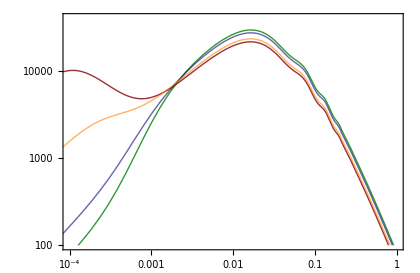

```mathematica
LogLogPlot[{
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE111E221[[2]],
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE111nE221n[[2]],
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE1105E2205[[2]],
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE1105nE2205n[[2]]}//Evaluate,{k,10^-5,1.5},PlotRange->{{10^-4,1},{100,4*10^4}},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]],
Directive[Thick,Opacity[0.6],Orange]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [(\\text{Mpc} \\, h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = 1, \\ E_{22} = 1"],
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = -1, \\ E_{22} = -1"],
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = 0.5, \\ E_{22} = 0.5"],
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = -0.5, \\ E_{22} = -0.5"]},
 LegendLayout->{"Row",4},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->None],{0.55,0.35}],ImageSize->420]
```

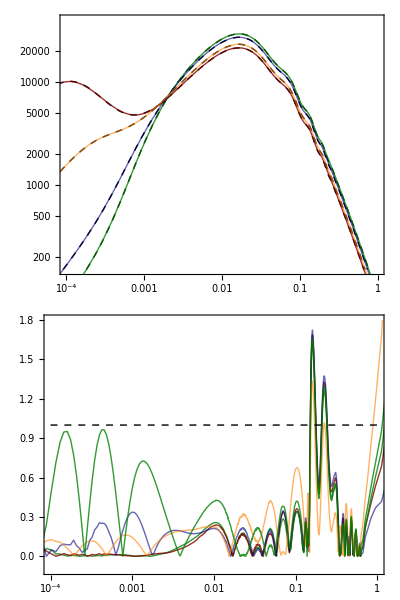

```mathematica
ListLogLogPlot[{DataE111E221,DataE111nE221n,DataE1105E2205,DataE1105nE2205n},Joined->True,PlotRange->{{10^-4,1},{150,4*10^4}},PlotStyle->Directive[{Dashed,Black,Thick}],Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} \\, h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->0.60,ImageSize->480];
LogLogPlot[{
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE111E221[[2]],
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE111nE221n[[2]],
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE1105E2205[[2]],
PMG[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE1105nE2205n[[2]]}//Evaluate,{k,10^-5,1.5},PlotRange->{{10^-4,1},{100,4*10^4}},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]],
Directive[Thick,Opacity[0.6],Orange]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k) \\, [(\\text{Mpc} \\, h^{-1})^3]"},BaseStyle->{FontFamily->"Times",FontSize->16},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = 1, \\ E_{22} = 1"],
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = -1, \\ E_{22} = -1"],
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = 0.5, \\ E_{22} = 0.5"],
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = -0.5, \\ E_{22} = -0.5"]},
 LegendLayout->{"Row",4},LabelStyle->{Black,Bold,15},LegendMarkerSize->20,LegendFunction->Frame],{0.52,0.325}],ImageSize->480];//Quiet
i=.;j=.;l=.;
Show[{%%%,%%},ImageSize->480,AspectRatio->0.6,ImagePadding->{{75,15},{0,0}}]//Quiet;
ListLogLinearPlot[{MAPEE110E221,MAPEE1105E2205,MAPEE111E221,MAPEE1105nE2205n,MAPEE111nE221n},Joined->True,PlotRange->{{10^-4,1},{-0.1,1.8}},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]],
Directive[Thick,Opacity[0.6],Orange]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","\\text{MAPE}(\\text{GA})"},BaseStyle->{FontFamily->"Times",FontSize->16},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]}},ImageSize->480,AspectRatio->0.3,ImagePadding->{{75,15},{50,0}}]//Quiet;
PlotPaper=Column[{%%,%},Spacings->0]
```

```mathematica
Export["plk_late_Plot.pdf",PlotPaper]
```

plk_late_Plot.pdf

```mathematica
PkE110E221=Interpolation[DataE110E221];
PkE1105E2205=Interpolation[DataE1105E2205];
PkE111E221=Interpolation[DataE111E221];
PkE1105nE2205n=Interpolation[DataE1105nE2205n];
PkE111nE221n=Interpolation[DataE111nE221n];
```

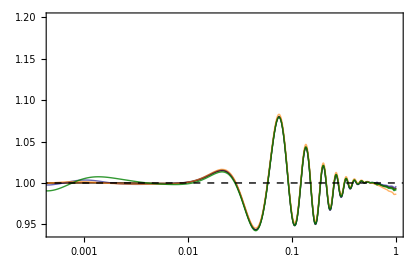

```mathematica
LogLinearPlot[{
PkE110E221[k]/PMGnw[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE110E221[[2]],
PkE1105E2205[k]/PMGnw[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE1105E2205[[2]],
PkE111E221[k]/PMGnw[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE111E221[[2]],
PkE1105nE2205n[k]/PMGnw[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE1105nE2205n[[2]],
PkE111nE221n[k]/PMGnw[k,h,ωb,ωm,ns,As,αMG,kT,βT,sMG,γMG,kMG,σMG]/.ParamsE111nE221n[[2]]},{k,10^-4,1},PlotRange->{{5*10^-4,1},{0.94,1.2}},PlotStyle->{Directive[Thick,Opacity[0.8],RGBColor[0,0.5,0]],Directive[Thick,Opacity[0.8],RGBColor[0.5,0,0]],Directive[Thick,Opacity[0.6],RGBColor[0,0,0.5]],
Directive[Thick,Opacity[0.6],Orange]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","O_\\text{lin}(k)"},BaseStyle->{FontFamily->"Times",FontSize->16},Epilog->{{Dashed,Thick,Line[{{Log[10^-4],1},{Log[10],1}}]}},ImageSize->420,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = 1, \\ E_{22} = 1"],
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = -1, \\ E_{22} = -1"],
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = 0.5, \\ E_{22} = 0.5"],
(MaTeX[#, Magnification -> 1.0] &)/@Style["E_{11} = -0.5, \\ E_{22} = -0.5"]},
 LegendLayout->{"Row",4},LabelStyle->{Black,Bold,15},LegendMarkerSize->20,LegendFunction->Frame],{0.26,0.63}]]
```